# Graphics Generator

Author : D. Hernández
For IPD436

## M/M/1 example

### Data preprocessing (values were obtained using the MarkovSolver, available in git)

```mathematica
πValues1   = {0.2000000000,0.1600000000,0.1280000000,0.1024000000,0.0819200000,0.0655360000,0.0524288000,0.0419430400,0.0335544320};
dataTable1 =Table[{i, πValues1[[i+1]]},{i,0,8}];
```

### Function evaluation and data exporting

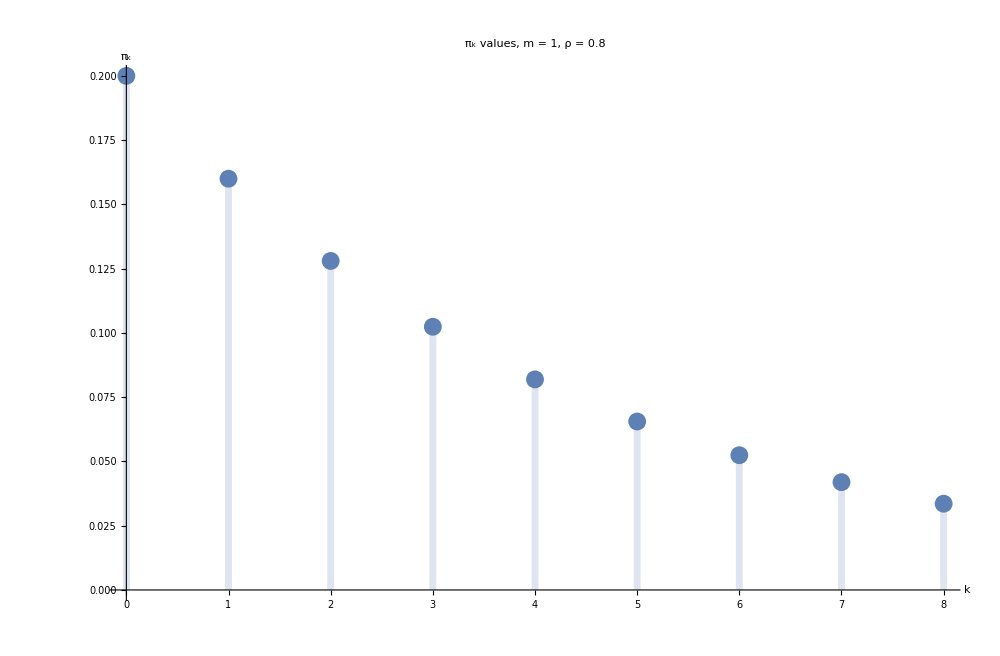
-Graphics- | k | π_k
0 | 0.2
1 | 0.16
2 | 0.128
3 | 0.1024
4 | 0.08192
5 | 0.065536
6 | 0.0524288
7 | 0.041943
8 | 0.0335544

```mathematica
plot1 = DiscretePlot[πValues1[[x+1]], {x, 0, 8}, PlotStyle-> Thickness[0.005], 
										AxesLabel->{HoldForm[k],HoldForm[Subscript[π, k]]}, 
										PlotLabel->RawBoxes[RowBox[{RowBox[{SubscriptBox["π","k"],"values"}],","," ",RowBox[{"m"," ","="," ","1"}],","," ",RowBox[{"ρ"," ","="," ","0.8"}]}]], 
										LabelStyle->{16,GrayLevel[0],Bold}, 
										ImageSize->{1000,656}, 
										AspectRatio->Full];
Grid[{{plot1, Grid[Join[{{"k", "π_k"}}, dataTable1], Alignment->Left, Frame->All]}}]
Export["Wolfram Mathematica/PNM_mm1.png", %];
```

## M/M/3 example

### Data preprocessing (values were obtained using the MarkovSolver, available in git)

```mathematica
πValues3   = {0.4471544715,0.3577235772,0.1430894309,0.0381571816,0.0101752484,0.0027133996,0.0007235732,0.0001929529,0.0000514541};
dataTable3 =Table[{i, πValues3[[i+1]]},{i,0,8}];
```

### Function evaluation and data exporting

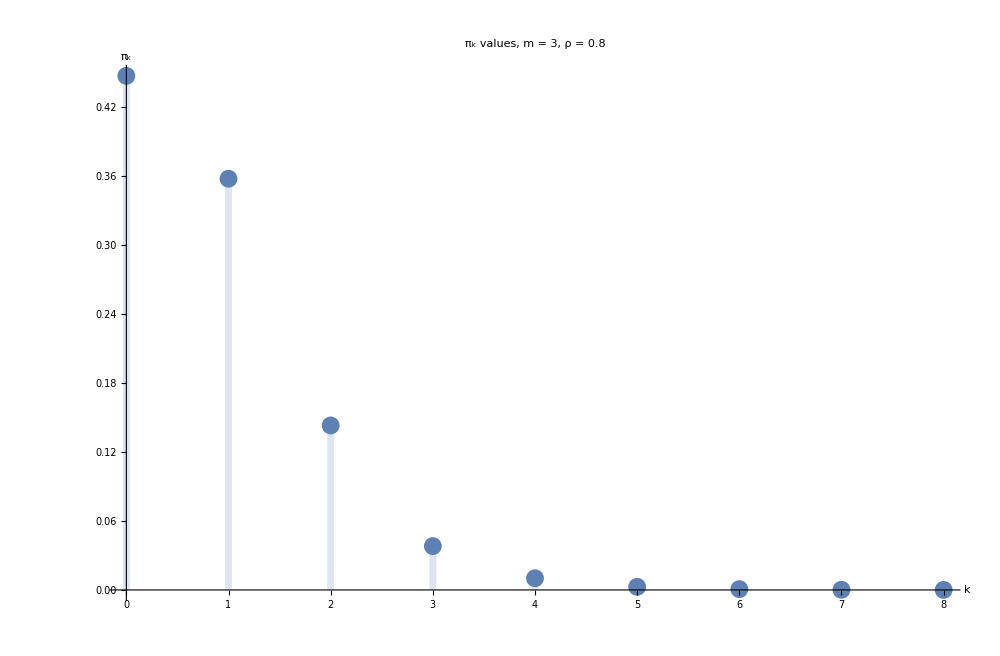
-Graphics- | k | π_k
0 | 0.447154
1 | 0.357724
2 | 0.143089
3 | 0.0381572
4 | 0.0101752
5 | 0.0027134
6 | 0.000723573
7 | 0.000192953
8 | 0.0000514541

```mathematica
plot3 = DiscretePlot[πValues3[[x+1]], {x, 0, 8}, PlotStyle-> Thickness[0.005], 
										AxesLabel->{HoldForm[k],HoldForm[Subscript[π, k]]}, 
										PlotLabel->RawBoxes[RowBox[{RowBox[{SubscriptBox["π","k"],"values"}],","," ",RowBox[{"m"," ","="," ","3"}],","," ",RowBox[{"ρ"," ","="," ","0.8"}]}]], 
										LabelStyle->{16,GrayLevel[0],Bold}, 
										ImageSize->{1000,656}, 
										AspectRatio->Full];
Grid[{{plot3, Grid[Join[{{"k", "π_k"}}, dataTable3], Alignment->Left, Frame->All]}}]
Export["Wolfram Mathematica/PNM_mm3.png", %];
```

## M/M/10 example

### Data preprocessing (values were obtained using the MarkovSolver, available in git)

```mathematica
πValues10 = {0.4493289641,0.3594631713,0.1437852685,0.0383427383,0.0076685477,0.0012269676,0.0001635957,0.0000186966,0.0000018697};
dataTable10 =Table[{i, πValues10[[i+1]]},{i,0,8}];
```

### Function evaluation and data exporting

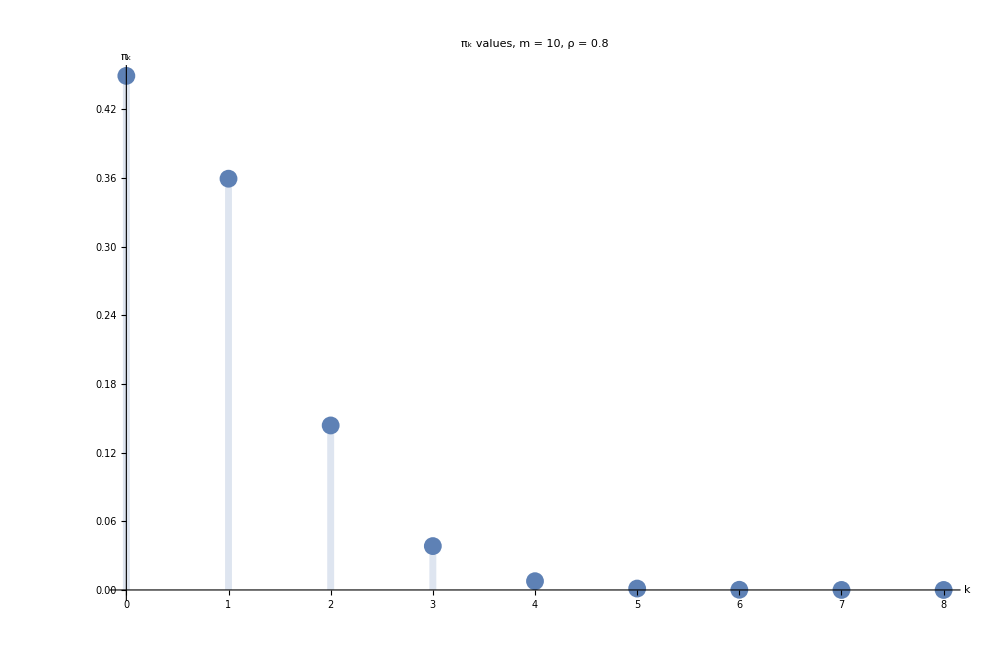
-Graphics- | k | π_k
0 | 0.449329
1 | 0.359463
2 | 0.143785
3 | 0.0383427
4 | 0.00766855
5 | 0.00122697
6 | 0.000163596
7 | 0.0000186966
8 | 1.8697×10^-6

```mathematica
plot10 = DiscretePlot[πValues10[[x+1]], {x, 0, 8}, PlotStyle-> Thickness[0.005], 
										AxesLabel->{HoldForm[k],HoldForm[Subscript[π, k]]}, 
										PlotLabel->RawBoxes[RowBox[{RowBox[{SubscriptBox["π","k"],"values"}],","," ",RowBox[{"m"," ","="," ","10"}],","," ",RowBox[{"ρ"," ","="," ","0.8"}]}]], 
										LabelStyle->{16,GrayLevel[0],Bold}, 
										ImageSize->{1000,656}, 
										AspectRatio->Full];
Grid[{{plot10, Grid[Join[{{"k", "π_k"}}, dataTable10], Alignment->Left, Frame->All]}}]
Export["Wolfram Mathematica/PNM_mm10.png", %];
```

## M/G/1 example

### Data preprocessing (values were obtained using the MarkovSolver, available in git)

```mathematica
importπData[filename_]:=Module[{πData},
								πData =DeleteCases[Flatten[Import[filename, "CSV"]], _String];
								Table[{i, πData[[i+1]]}, {i,0,Length[πData]-1}]]
generatePlot[πTable_, dist_, ρ_]:= DiscretePlot[πTable[[x+1]][[2]], {x, 0, Length[πTable]-1}, 
										PlotStyle-> Thickness[0.005], 
										AxesLabel->{HoldForm[k],HoldForm[Subscript[π, k]]}, 
										PlotLabel->RawBoxes[RowBox[{RowBox[{SubscriptBox["π","k"],"values"}],","," ",
																RowBox[{dist," ","distribution"}],","," ",
																RowBox[{"ρ"," ","="," ",ToString[ρ]}]}]], 
										LabelStyle->{16,GrayLevel[0],Bold}, 
										ImageSize->{1000,656}, 
										AspectRatio->Full];
plotπData[filename_, dist_, ρ_]:= Module[{πTable, plot, grid},
									πTable = importπData[filename];
									plot = generatePlot[πTable, dist, ρ];
									grid = Grid[{{plot, Grid[Join[{{"k", "π_k"}}, πTable], Alignment->Left, Frame->All]}}];
									Print[grid];
									Export[FileNameJoin[{NotebookDirectory[], FileBaseName[filename] <> ".png"}], grid]]
```

### Function evaluation and data exporting

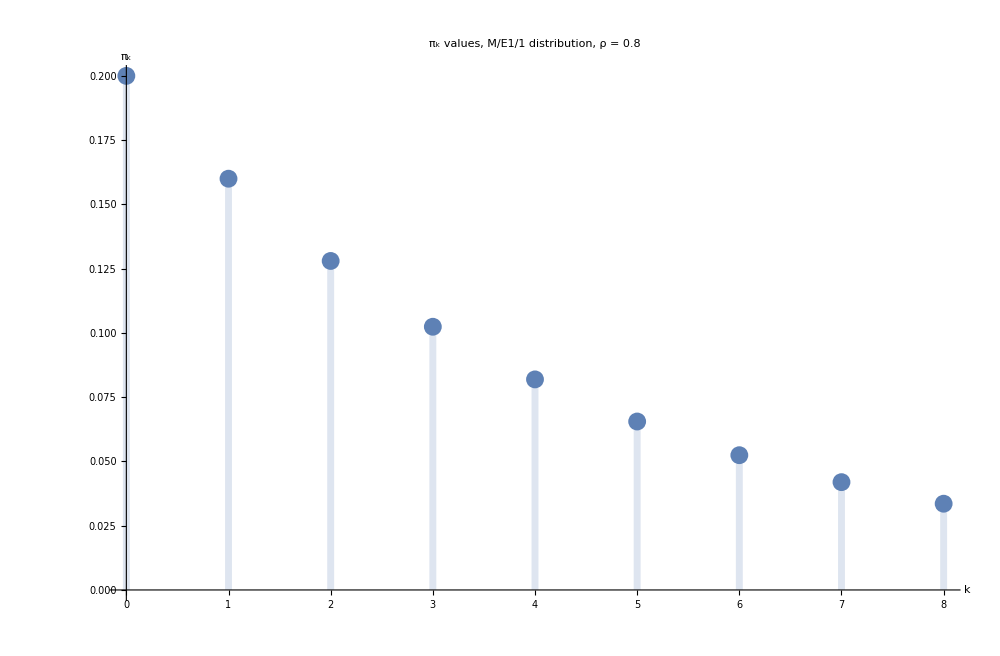
-Graphics- | k | π_k
0 | 0.2
1 | 0.16
2 | 0.128
3 | 0.1024
4 | 0.08192
5 | 0.065536
6 | 0.0524288
7 | 0.041943
8 | 0.0335544

```mathematica
plotπData["mer1_1_rho_08.csv", "M/E1/1", 0.8]
```